```mathematica
Clear[t];rE=1;rM=1.5237;μsAU=0.000295912;vE=√(μsAU/rE);vM=√(μsAU/rM);vpiEM=√(μsAU (2/rE-2/(rE+rM)));deltavEM=vpiEM-vE;
solmfunc[theta0_,alpha_]:=NDSolve[{r1''[t]-r1[t]*th1'[t]^2==-μsAU/ r1[t]^2,r1[t]*th1''[t]+2*r1'[t]*th1'[t]==0,r2''[t]-r2[t]*th2'[t]^2==-μsAU /r2[t]^2,r2[t]*th2''[t]+2*r2'[t]*th2'[t]==0,r3''[t]-r3[t]*th3'[t]^2==-μsAU /r3[t]^2,r3[t]*th3''[t]+2*r3'[t]*th3'[t]==0,r1[0]==rE,th1[0]==0,r1'[0]==0,th1'[0]==√(μsAU/rE)/rE,r2[0]==rM,th2[0]==0,r2'[0]==0,th2'[0]==
√(μsAU/rM)/rM,r3[0]==rE,th3[0]==0,r3'[0]==alpha*deltavEM Sin[theta0],th3'[0]==vE+alpha*deltavEM Cos[theta0]},{r1,th1,r2,th2,r3,th3},{t,0,12000}]
```

```mathematica
{{rsol1,thsol1,rsol2,thsol2,rsol3,thsol3}}={r1,th1,r2,th2,r3,th3}/.solmfunc[0,1.5]
```

{{InterpolatingFunction[{{0., 12000.}}, <>],InterpolatingFunction[{{0., 12000.}}, <>],InterpolatingFunction[{{0., 12000.}}, <>],InterpolatingFunction[{{0., 12000.}}, <>],InterpolatingFunction[{{0., 12000.}}, <>],InterpolatingFunction[{{0., 12000.}}, <>]}}

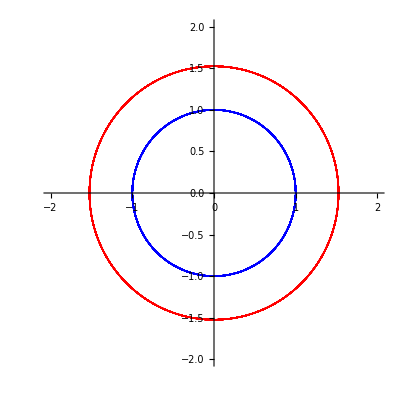

```mathematica
Show[
ParametricPlot[{rsol1[t]*Cos[thsol1[t]],rsol1[t]*Sin[thsol1[t]]},{t,0,12000},PlotStyle-> {Blue,Thick},AspectRatio-> 1,PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[{rsol2[t]*Cos[thsol2[t]],rsol2[t]*Sin[thsol2[t]]},{t,0,12000},PlotStyle-> {Red,Thick},PlotRange->{{-2,2},{-2,2}}]]
```

```mathematica
posxearth[Z_]:=rsol1[Z]*Cos[thsol1[Z]]
posyearth[Z_]:=rsol1[Z]*Sin[thsol1[Z]]
posxmars[Z_]:= rsol2[Z]*Cos[thsol2[Z]]
posymars[Z_]:=rsol2[Z]*Sin[thsol2[Z]]

earthx=Table[posxearth[t],{t,12000}];
```

```mathematica
marsx=Table[posxmars[t],{t,12000}];
```

```mathematica
combx=Riffle[earthx,marsx];
```

```mathematica
earthy=Table[posyearth[t],{t,12000}];
```

```mathematica
marsy=Table[posymars[t],{t,12000}];
```

```mathematica
comby=Riffle[earthy,marsy];
```

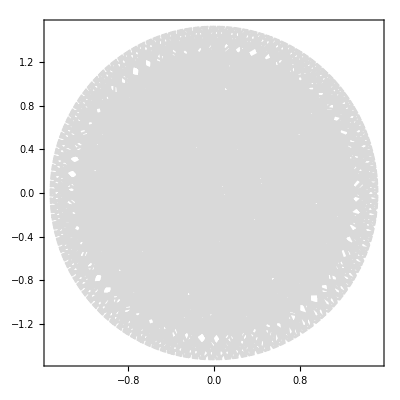

```mathematica
athing=ListLinePlot[Table[{combx[[n]],comby[[n]]},{n,0,12000,11}],Frame->True, AspectRatio->1, PlotStyle->LightGray]
```

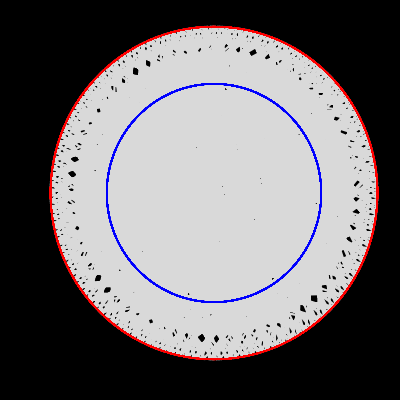

```mathematica
finalthing=Show[athing,
ParametricPlot[{rsol1[t]*Cos[thsol1[t]],rsol1[t]*Sin[thsol1[t]]},{t,0,12000},PlotStyle-> {Blue,Thick},AspectRatio-> 1,PlotRange->{{-2,2},{-2,2}}],
ParametricPlot[{rsol2[t]*Cos[thsol2[t]],rsol2[t]*Sin[thsol2[t]]},{t,0,12000},PlotStyle-> {Red,Thick},PlotRange->{{-2,2},{-2,2}}], Frame->True,ImageSize->Full, Background-> Black]
```

```mathematica
Export["finalplot.gif",finalthing]
```

finalplot.gif